First, let’s look at the data.  Here are the energies for first three bands, plus for the free particle.  Note the format here is {Level, Energy}.

```mathematica
Band1={{1,1.14},{2,1.17},{3,1.24},{4,1.31},{5,1.4},{6,1.52},{7,1.63},{8,1.72},{9,1.82},{10,1.87}};
Band2={{11,4.73},{12,4.87},{13,5.14},{14,5.41},{15,5.73},{16,6.15},{17,6.53},{18,6.88},{19,7.25},{20,7.49}};
Band3={{21,11.17},{22,11.48},{23,11.99},{24,12.54},{25,13.2},{26,13.96},{27,14.69},{28,15.42},{29,16.21},{30,16.79}};
FreeParticle={{10,1.86},{20,7.43},{30,16.72}};
```

To begin, let’s plot all three bands, and add horizontal lines at the free particle energies:

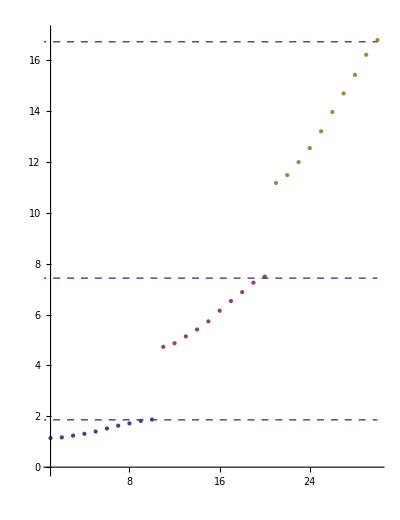

```mathematica
Show[
ListPlot[{Band1,Band2,Band3},PlotStyle->PointSize[Medium],PlotRange->{0,17}],
Plot[FreeParticle[[All,2]],{x,0,30},PlotStyle-> Dashed],
AspectRatio->1.3]
```

Nice.  Now, to guide the eyes, let’s join the points with lines, and also add a parabola going through the free particle points.  The easiest way to do this last is to fit a quadratic to the points using Mathematica’s Fit function:

```mathematica
Parabola=Fit[FreeParticle, {1,x,x^2}, x]
```

0.01-0.001 x+0.0186 x^2

Now add that to the plot:

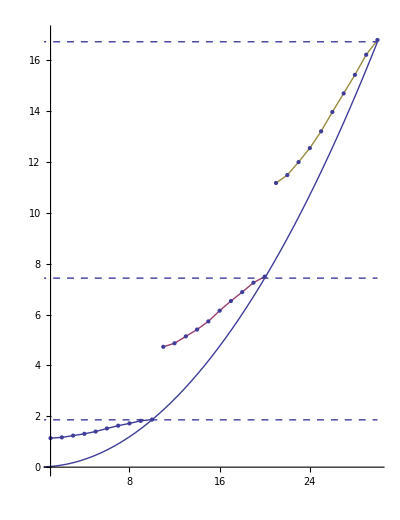

```mathematica
Show[
ListPlot[{Band1,Band2,Band3},PlotStyle->PointSize[Medium],Joined->True,InterpolationOrder->1,Mesh->Full,PlotRange->{0,17}],
Plot[FreeParticle[[All,2]],{x,0,30},PlotStyle-> Dashed],
Plot[Parabola,{x,0,30}],
AspectRatio->1.3]
```

Not bad.  Now let’s add some shading to mark the bands (using RegionPlot) and generally pretty-fy:

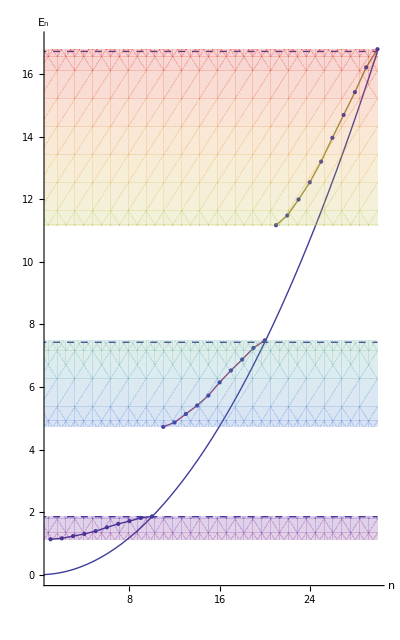

```mathematica
Show[
ListPlot[{Band1,Band2,Band3},PlotStyle->PointSize[Medium],Joined->True,InterpolationOrder->1,Mesh->Full,PlotRange->{0,17}],
Plot[FreeParticle[[All,2]],{x,0,30},PlotStyle-> Dashed],
Plot[Parabola,{x,0,30}],
RegionPlot[First[Band1][[2]]<y<Last[Band1][[2]]||First[Band2][[2]]<y<Last[Band2][[2]]||First[Band3][[2]]<y<Last[Band3][[2]],
{x,0,30},{y,0,17},BoundaryStyle->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.2]],
AspectRatio->1.6,
AxesOrigin->{0,0},
AxesLabel->{"n","E_n"},
ImageSize->{72 10}
]
```

Nice!

OK, what i’d like to do now is make a mirror image of these plots and read them as pictures of E(q_n), with q_n the crystal momentum of the state.  To do this we need to build lists of the data for n<0, which we can do with Map, plus a Reverse to get the order right:

```mathematica
Band1R=Reverse[Map[{-#[[1]],#[[2]]}&,Band1]];
Band2R=Reverse[Map[{-#[[1]],#[[2]]}&,Band2]];
Band3R=Reverse[Map[{-#[[1]],#[[2]]}&,Band3]];
```

While we’re at it, we should mirror the free particle data, too, and re-fit the Parabola:

```mathematica
FreeParticleR=Map[{-#[[1]],#[[2]]}&,FreeParticle];
Parabola = Fit[Join[FreeParticleR,FreeParticle], {1,x,x^2}, x];
```

So now let’s plot the full data set:

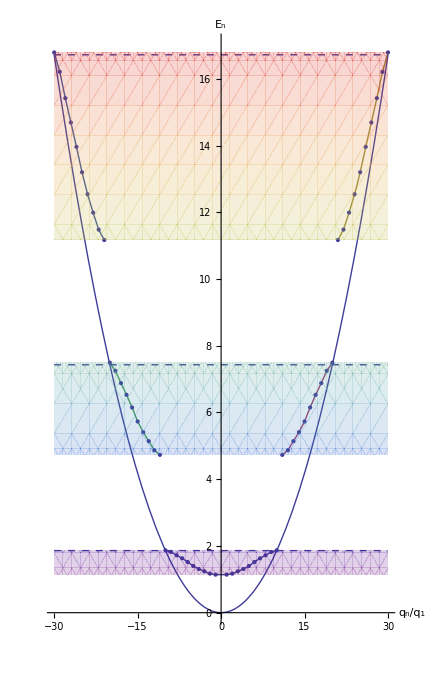

```mathematica
Show[
ListPlot[{Join[Band1R,Band1],Band2,Band3,Band2R,Band3R},PlotStyle->PointSize[Medium],Joined->True,InterpolationOrder->1,Mesh->Full,PlotRange->{0,17}],
Plot[FreeParticle[[All,2]],{x,-30,30},PlotStyle-> Dashed],
Plot[Parabola,{x,-30,30}],
RegionPlot[First[Band1][[2]]<y<Last[Band1][[2]]||First[Band2][[2]]<y<Last[Band2][[2]]||First[Band3][[2]]<y<Last[Band3][[2]],
{x,-30,30},{y,0,17},BoundaryStyle->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.2]],
AspectRatio->1.58,
AxesOrigin->{0,0},
AxesLabel->{"q_n/q_1","E_n"},
ImageSize->{72 6,72 9.2}
]
```

Very pretty.

Finally, recalling that the crystal momentum is only defined up to an inverse lattice spacing,  q L == q L + 2 π N,  let’s replot this result over a single domain of q.  To do so we need to again rebuild the lists:

```mathematica
Band2FD = Map[{#[[1]]-21,#[[2]]}&,Band2];
Band2FDR = Map[{#[[1]]+21,#[[2]]}&,Band2R];
Band3FD = Map[{#[[1]]-20,#[[2]]}&,Band3];
Band3FDR = Map[{#[[1]]+20,#[[2]]}&,Band3R];
```

We’ll also need to include the shifted parabola, so:

```mathematica
Parabola20p=parabolaB/.x->x+20;
Parabola20m=parabolaB/.x->x-20;
```

Putting this all together,

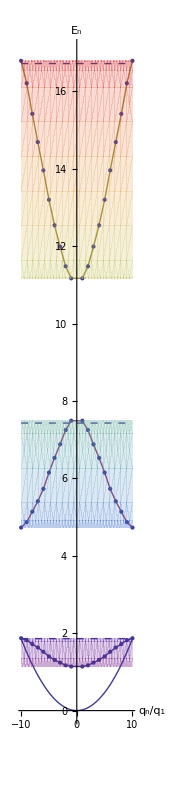

```mathematica
Show[
ListPlot[{Join[Band1R,Band1],Join[Band2FD,Band2FDR],Join[Band3FDR,Band3FD]},PlotStyle->PointSize[Medium],Joined->True,InterpolationOrder->1,Mesh->Full,PlotRange->{0,17}],
Plot[FreeParticle[[All,2]],{x,-10,10},PlotStyle-> Dashed],
Plot[{Parabola,Parabola20p,Parabola20m},{x,-10,10}],
RegionPlot[First[Band1][[2]]<y<Last[Band1][[2]]||First[Band2][[2]]<y<Last[Band2][[2]]||First[Band3][[2]]<y<Last[Band3][[2]],
{x,-10,10},{y,0,17},BoundaryStyle->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.2]],
AspectRatio->4.6,
AxesOrigin->{0,0},
AxesLabel->{"q_n/q_1","E_n"},
ImageSize->{72 2.4,72 9.2}
]
```

Just for fun, let’s see if there’s enough resolution to see the variation of the level spacing within the band.

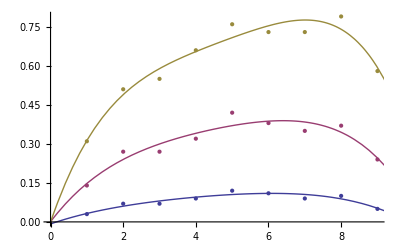

```mathematica
dif1=Band1[[2;;10,2]]-Band1[[1;;9,2]];
dif2=Band2[[2;;10,2]]-Band2[[1;;9,2]];
dif3=Band3[[2;;10,2]]-Band3[[1;;9,2]];

DifFit1 = Fit[dif1, {1,x,x^2,x^3,x^4}, x];
DifFit2 = Fit[dif2, {1,x,x^2,x^3,x^4}, x];
DifFit3 = Fit[dif3, {1,x,x^2,x^3,x^4}, x];

Show[
ListPlot[{dif1,dif2,dif3}],
Plot[{DifFit1,DifFit2,DifFit3},{x,0,10}]
]
```